### Part I: Matrix Mechanics

#### Representation of Operator

Definition of an operator:

Ô=∑_(i,j) i O_(i,j)j.

Action of an operator on a basis state:

Ô j=∑_i iO_ij.

Matrix representation of an operator

Ô≏(O_11 | O_12 | ⋯
O_21 | O_22 | ⋯
⋮ | ⋮ | ⋱).

Method: make a table, fill in the matrix element. 
Indexing rule: from top to left.

Ô j→O_ij i⇒  | ⋯ | j | ⋯
⋮ |   | ↓ |  
i | ← | O_ij |  
⋮ |   |   |

Write down matrix representations of the following single-qubit operators X̂, Ŷ, Ẑ: 
X̂ 0=1, X̂ 1=0;
Ŷ 0=ⅈ 1, Ŷ 1=-ⅈ0;
Ẑ 0=0, Ẑ 1=-1.

Using the table method:

|   | 0 | 1
  |   |   |  
0 |   |   |  
1 |   |   |  ⇒^(X̂ 0=1)  |   | 0 | 1
  |   | ↓ |  
0 |   | ↓ |  
1 | ← | 1 |  ⇒^(X̂ 1=0)  |   | 0 | 1
  |   |   | ↓
0 | ← | ← | 1
1 |   | 1 |  
therefore:X̂≏(0 | 1
1 | 0).

|   | 0 | 1
  |   |   |  
0 |   |   |  
1 |   |   |  ⇒^(Ŷ 0=ⅈ1)  |   | 0 | 1
  |   | ↓ |  
0 |   | ↓ |  
1 | ← | ⅈ |  ⇒^(Ŷ 1=-ⅈ0)  |   | 0 | 1
  |   |   | ↓
0 | ← | ← | -ⅈ
1 |   | ⅈ |  
therefore:Ŷ≏(0 | -ⅈ
ⅈ | 0).

|   | 0 | 1
  |   |   |  
0 |   |   |  
1 |   |   |  ⇒^(Ẑ 0=0)  |   | 0 | 1
  |   | ↓ |  
0 | ← | 1 |  
1 |   |   |  ⇒^(Ẑ 1=-1)  |   | 0 | 1
  |   |   | ↓
0 |   | 1 | ↓
1 | ← | ← | -1
therefore:Ẑ≏(1 | 0
0 | -1).

Consider a system of two qubits, called A and B. Write down the matrix representation of (X̂)_A, (Ẑ)_B, and (X̂)_A(Ẑ)_B in the {00, 01, 10, 11} basis.

Rules for (X̂)_A:

(X̂)_A 0?=1?, (X̂)_A 1?=0?.

Method I: Filling the table

| 00 | 01 | 10 | 11
00 |   |   | 1 |  
01 |   |   |   | 1
10 | 1 |   |   |  
11 |   | 1 |   |  ⇒(X̂)_A≏(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

Method II: Tensor product

((X̂)_A)_(4×4)=(X̂)_(2×2)⊗𝟙_(2×2)
≏(0 | 1
1 | 0)⊗(1 | 0
0 | 1)
=(0(1 | 0
0 | 1) | 1(1 | 0
0 | 1)
1(1 | 0
0 | 1) | 0(1 | 0
0 | 1))
=(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0).

Rules for (Ẑ)_B:

(Ẑ)_B?0=?0, (Ẑ)_B?1=-?1.

Method I: Filling the table

| 00 | 01 | 10 | 11
00 | 1 |   |   |  
01 |   | -1 |   |  
10 |   |   | 1 |  
11 |   |   |   | -1⇒(Ẑ)_B≏(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

Method II: Tensor product

((Ẑ)_B)_(4×4)=𝟙_(2×2)⊗(Ẑ)_(2×2)
≏(1 | 0
0 | 1)⊗(1 | 0
0 | -1)
=(1(1 | 0
0 | -1) | 0(1 | 0
0 | -1)
0(1 | 0
0 | -1) | 1(1 | 0
0 | -1))
=(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1).

Rules for (X̂)_A(Ẑ)_B:

(X̂)_A(Ẑ)_B 00=10,
(X̂)_A(Ẑ)_B 01=-11,
(X̂)_A(Ẑ)_B 10=00,
(X̂)_A(Ẑ)_B 11=-01.

Method I: Filling the table

| 00 | 01 | 10 | 11
00 |   |   | 1 |  
01 |   |   |   | -1
10 | 1 |   |   |  
11 |   | -1 |   |  ⇒(X̂)_A(Ẑ)_B≏(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0).

Method II: Tensor product

((X̂)_A(Ẑ)_B)_(4×4)=(X̂)_(2×2)⊗(Ẑ)_(2×2)
≏(0 | 1
1 | 0)⊗(1 | 0
0 | -1)
=(0(1 | 0
0 | -1) | 1(1 | 0
0 | -1)
1(1 | 0
0 | -1) | 0(1 | 0
0 | -1))
=(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0).

Method III: Matrix multiplication

(X̂)_A≏(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0), (Ẑ)_B≏(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1),

therefore,

(X̂)_A(Ẑ)_B≏(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)
=(0 | 0 | 1 | 0
0 | 0 | 0 | -1
1 | 0 | 0 | 0
0 | -1 | 0 | 0).

#### Time Evolution

Given a Hamiltonian Ĥ

Ĥ=∑_n n E_n n,

the time-evolution unitary is given by

Û=ⅇ^(-ⅈ Ĥ t)=∑_n n ⅇ^(-ⅈ E_n t)n.

State evolution (Schrödinger picture)

ψ | → | Û ψ
∥ |   | ∥
∑_n ψ_n n | → | ∑_n ψ_n ⅇ^(-ⅈ E_n t)n

Operator evolution (Heisenberg picture)

Ô | → | (Û)^†Ô Û
∥ |   | ∥
∑_mn O_mn mn | → | ∑_mn O_mn ⅇ^(ⅈ (E_m-E_n)t)mn

Expectation value evolution (either pictures)

⟨O⟩_0 | → | ⟨O⟩_t
∥ |   | ∥
ψ Ô ψ | → | ψ(Û)^†Ô Û ψ
∥ |   | ∥
∑_mn ψ_m^*O_mn ψ_n | → | ∑_mn ψ_m^*O_mn ψ_n ⅇ^(ⅈ (E_m-E_n)t)

Show that the time average of expectation value 
OverBar[⟨O⟩]=lim_(T→∞) 1/T∫_(-T/2)^(T/2) ⅆt⟨O⟩_t
only depends on the diagonal matrix elements of Ô in the eigenbasis of Ĥ.

OverBar[⟨O⟩]=lim_(T→∞) 1/T∫_(-T/2)^(T/2) ⅆt⟨O⟩_t
=lim_(T→∞) 1/T∫_(-T/2)^(T/2) ⅆt ∑_mn ψ_m^*O_mn ψ_n ⅇ^(ⅈ (E_m-E_n)t)
=∑_mn ψ_m^*O_mn ψ_n lim_(T→∞) 1/T∫_(-T/2)^(T/2) ⅆt ⅇ^(ⅈ (E_m-E_n)t)
=∑_mn ψ_m^*O_mn ψ_n lim_(T→∞) 2/((E_m-E_n)T)sin(((E_m-E_n)T)/2),

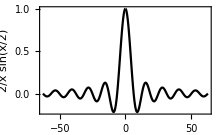

```mathematica
Plot[2/x Sin[x/2],{x,-20π,20π},FrameLabel->{"\!\(x\)","\!\(2\/x sin(x\/2)\)"},PlotStyle->Black,PlotRange->All,ImageSize->220]
```

OverBar[⟨O⟩]=∑_mn ψ_m^*O_mn ψ_n δ_mn
=∑_n ψ_n^*O_nn ψ_n
=∑_n O_nn p_n,

where O_nn is the diagonal matrix element and p_n=(|ψ_n|)^2 is the probability for the system to be in the state n. Key: off-diagonal matrix elements do not contribute.

#### Measurement

Given a Hermitian observable Ô

Ô=∑_k O_k O_k O_k.

Measure the observable Ô on the state ψ:

Possible measurement outcomes: O_k (eigenvalues)

Probability to observe a particular outcome O_k:

p(O_k|ψ)=(|O_kψ|)^2.

After observing O_k, the state collapses to:

If there is no degeneracy

ψ→O_k .

If there is degeneracy

ψ→α_m O_k,m,

where α_m∝O_k,mψ followed by normalization.

Consider a two-qubit system, initially in arbitrary state. Measure (X̂)_A(X̂)_B and (Ŷ)_A(Ŷ)_B simultaneously. Observe X_A X_B=-1 and Y_A Y_B=+1. What is the post-measurement final state?

Let ψ be the final state, it must be eigenstates of both (X̂)_A(X̂)_B and (Ŷ)_A(Ŷ)_B with eigenvalues -1 and +1 respectively, i.e.

(X̂)_A(X̂)_B ψ=-ψ,
(Ŷ)_A(Ŷ)_B ψ=+ψ.

To solve these equations, first write down matrix representations of operators

(X̂)_A(X̂)_B≏(0 | 1
1 | 0)⊗(0 | 1
1 | 0)=(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0),
(Ŷ)_A(Ŷ)_B≏(0 | -ⅈ
ⅈ | 0)⊗(0 | -ⅈ
ⅈ | 0)=(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0).

Then assume

ψ≏(ψ_00
ψ_01
ψ_10
ψ_11),

Eq. (DisplayFormulaNumbered) implies

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)(ψ_00
ψ_01
ψ_10
ψ_11)=-(ψ_00
ψ_01
ψ_10
ψ_11)
⇒(ψ_11
ψ_10
ψ_01
ψ_00)=-(ψ_00
ψ_01
ψ_10
ψ_11),
(0 | 0 | 0 | -1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
-1 | 0 | 0 | 0)(ψ_00
ψ_01
ψ_10
ψ_11)=(ψ_00
ψ_01
ψ_10
ψ_11)
⇒(-ψ_11
ψ_10
ψ_01
-ψ_00)=(ψ_00
ψ_01
ψ_10
ψ_11).

This means

ψ_00=-ψ_11, ψ_01=0, ψ_10=0.

One (normalized) solutions is

ψ≏(ψ_00
ψ_01
ψ_10
ψ_11)=1/(√2)(1
0
0
-1)

or expressed as

ψ=1/(√2)(00-11),

which is the post-measurement final state (that is consistent with all observations).

### Par II: Algebraic Methods

#### Harmonic Oscillator

Annihilation and creation operators

{ | â=1/(√2)(x̂+ⅈ p̂)
(â)^†=1/(√2)(x̂-ⅈ p̂), { | x̂=1/(√2)(â+(â)^†)
p̂=1/(√2 ⅈ)(â-(â)^†).

They satisfies the commutation relation

[x̂,p̂]=ⅈ 𝟙⇔[â,(â)^†]=𝟙.

Number operator

n̂=(â)^†â.

It defines a discrete spectrum n̂ n=nn for n∈ℕ. Such that

â n=√n n-1,
(â)^†n=√(n+1)n+1.

Hamiltonian

Ĥ=1/2 ℏ ω ((p̂)^2+(x̂)^2)=ℏ ω (n̂+𝟙/2).

Eigen energies

E_n=ℏ ω(n+1/2).

Every eigenstate n can be raised from the ground state by

n=1/(√(n!))((â)^†)^n 0.

Calculate n x̂ p̂ n.

Always use creation/annihilation operator to evaluate expectation values on the boson number eigenstate (energy eigenstate).

n x̂ p̂ n=n 1/(√2)(â+(â)^†)1/(√2 ⅈ)(â-(â)^†)n
=1/(2ⅈ)n(â â-â(â)^†+(â)^†â-(â)^†(â)^†)n
=1/(2ⅈ)n(-â(â)^†+(â)^†â)n
=1/(2ⅈ)n(-[â,(â)^†])n
=1/(2ⅈ)n(-𝟙)n
=1/(2ⅈ)(-1)
=ⅈ/2.

Consider 2D harmonic oscillator, described by 
Ĥ=1/2(p̂)^2+1/2(x̂)^2,
where p̂=((p̂)_1,(p̂)_2) and x̂=((x̂)_1,(x̂)_2) with [(x̂)_i,(x̂)_j]=[(p̂)_i,(p̂)_j]=0 and [(x̂)_i,(p̂)_j]=ⅈ δ_ij 𝟙. Find the eigen energies of Ĥ and the corresponding degeneracies.

Introduce two set of creation/annihilation operators

{ | (â)_i=1/(√2)((x̂)_i+ⅈ OverHat[p_i])
(â)_i^†=1/(√2)((x̂)_i-ⅈ (p̂)_i).

Commutation relations

[(â)_i,(â)_j]=[(â)_i^†,(â)_j^†]=0, [(â)_i,(â)_j^†]=δ_ij 𝟙

indicates that they are independent boson modes.

Hamiltonian

Ĥ=1/2(p̂)^2+1/2(x̂)^2
=1/2((p̂)_1^2+(x̂)_1^2)+1/2((p̂)_2^2+(x̂)_2^2)
=((n̂)_1+𝟙/2)+((n̂)_2+𝟙/2)
=(n̂)_1+(n̂)_2+𝟙

where (n̂)_i:=(â)_i^†(â)_i is the number operator for the boson mode i.

Since (n̂)_1 and (n̂)_2 are commuting operators, the eigenstate of Ĥ will be the joint eigenstate of (n̂)_1 and (n̂)_2, labeled by their corresponding quantum numbers n_1,n_2∈ℕ:

(n̂)_1 n_1,n_2=n_1 n_1,n_2,
(n̂)_2 n_1,n_2=n_2 n_1,n_2.

On these eigenstates, the eigenvalue of Ĥ will be given by

E=n_1+n_2+1.

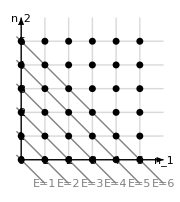

```mathematica
Block[{n=5,a=0.2},Graphics[{{Gray,Table[{Line[{{m+1,-1},{-a,m+a}}],Text[StringTemplate["\!\(E=`1`\)"][m+1],{m+1,-1},{-1,0},{1,-1}]},{m,0,n}]},{LightGray,AbsoluteThickness[1],{#,GeometricTransformation[#,ReflectionTransform[{1,-1},{0,0}]]}&@(Translate[Line[{#,0}&/@{0,n+1}],{0,#}]&/@Range[n])},{Arrowheads[0.08],Rotate[Arrow[{#,0}&/@{0,n+1}],π #/2,{0,0}]&/@{0,1}},{AbsolutePointSize[5],Table[Point[{n1,n2}],{n1,0,n},{n2,0,n}]},{Table[Text[n1,{n1,0},{0,1.2}],{n1,n}],Table[Text[n2,{0,n2},{2,0}],{n2,n}],Text[0,{0,0},{2,0.8}]},{Text["\!\(n\_1\)",{n+1,0},{0,1}],Text["\!\(n\_2\)",{0,n+1},{1.5,0}]}},ImageSize->180]]
```

So the eigen energies and the corresponding degeneracies are

E | 1 | 2 | 3 | ⋯
deg. | 1 | 2 | 3 | ⋯

Following (Exc Exercise). Define (Ŝ)_1=1/2((x̂)_1(x̂)_2+(p̂)_1(p̂)_2), find the matrix representation of (Ŝ)_1 in the E=2 subspace

The E=2 subspace is spanned by the following basis

{2,0, 1,1, 0,2}.

To represent (Ŝ)_1:

Rewrite it in terms of creation/annihilation operators

(Ŝ)_1=1/2((x̂)_1(x̂)_2+(p̂)_1(p̂)_2)
=1/2(1/(√2)((â)_1+(â)_1^†)1/(√2)((â)_2+(â)_2^†)+1/(√2 ⅈ)((â)_1-(â)_1^†)1/(√2 ⅈ)((â)_2-(â)_2^†))
=1/4(((â)_1+(â)_1^†)((â)_2+(â)_2^†)-((â)_1-(â)_1^†)((â)_2-(â)_2^†))
=1/4(((â)_1(â)_2+(â)_1^†(â)_2+(â)_1(â)_2^†+(â)_1^†(â)_2^†)-((â)_1(â)_2-(â)_1^†(â)_2-(â)_1(â)_2^†+(â)_1^†(â)_2^†))
=1/2((â)_1^†(â)_2+(â)_2^†(â)_1).

Enumerate the action of (Ŝ)_1 on the basis states,

(Ŝ)_1 2,0=1/2((â)_1^†(â)_2+(â)_2^†(â)_1)2,0
=1/2((â)_1^†(â)_2 2,0+(â)_2^†(â)_1 2,0)
=1/2(â)_2^†(â)_1 2,0
=(√2)/2(â)_2^†1,0
=1/(√2)1,1,

(Ŝ)_1 1,1=1/2((â)_1^†(â)_2+(â)_2^†(â)_1)1,1
=1/2((â)_1^†(â)_2 1,1+(â)_2^†(â)_1 1,1)
=1/2((â)_1^†1,0+(â)_2^†0,1)
=(√2)/2(2,0+0,2)
=1/(√2)2,0+1/(√2)0,2

(Ŝ)_1 0,2=1/2((â)_1^†(â)_2+(â)_2^†(â)_1)0,2
=1/2((â)_1^†(â)_2 0,2+(â)_2^†(â)_1 0,2)
=1/2(â)_1^†(â)_2 0,2
=(√2)/2(â)_1^†0,1
=1/(√2)1,1.

Fill the table to construct matrix representation

| 2,0 | 1,1 | 0,2
2,0 |   |   |  
1,1 |   |   |  
0,2 |   |   |  
⇒^((Ŝ)_1 2,0=1/(√2)1,1)  | 2,0 | 1,1 | 0,2
2,0 |   |   |  
1,1 | 1/(√2) |   |  
0,2 |   |   |  
⇒^((Ŝ)_1 1,1=1/(√2)2,0+1/(√2)0,2)  | 2,0 | 1,1 | 0,2
2,0 |   | 1/(√2) |  
1,1 | 1/(√2) |   |  
0,2 |   | 1/(√2) |  
⇒^((Ŝ)_1 0,2=1/(√2)1,1)  | 2,0 | 1,1 | 0,2
2,0 |   | 1/(√2) |  
1,1 | 1/(√2) |   | 1/(√2)
0,2 |   | 1/(√2) |  .

Therefore, the matrix representation of (Ŝ)_1 is

(Ŝ)_1≏1/(√2)(0 | 1 | 0
1 | 0 | 1
0 | 1 | 0).

#### Angular Momentum

Angular momentum operator Ĵ=((Ĵ)_1,(Ĵ)_2,(Ĵ)_3) is defined by the commutation relation

[(Ĵ)_a,(Ĵ)_b]=ⅈ ϵ_abc(Ĵ)_c.

Based on Ĵ, we can define

The total angular momentum operator

(Ĵ)^2=(Ĵ)_1^2+(Ĵ)_2^2+(Ĵ)_3^2.

The raising and lowering operators

(Ĵ)_±=(Ĵ)_1±ⅈ (Ĵ)_2.

They acts on the common eigen basis j,m as

(Ĵ)^2 j,m=j(j+1)j,m,
(Ĵ)_3 j,m=mj,m,
(Ĵ)_±j,m=√(j(j+1)-m(m±1))j,m±1,

where

j=0,1/2,1,3/2,…,
m=-j,-j+1,…,j-1,j.

Construct matrix representations of angular momentum operators (Ĵ)_1, (Ĵ)_2, (Ĵ)_3 in the spin-1 subspace.

In spin-1 subspace, j=1 and m=+1,0,-1.

Use (Ĵ)_3 j,m=mj,m, follow the table method

| 1,+1 | 1,0 | 1,-1
1,+1 | +1 |   |  
1,0 |   | 0  |  
1,-1 |   |   | -1

therefore,

(Ĵ)_3≏(1 | 0 | 0
0 | 0 | 0
0 | 0 | -1).

Use (Ĵ)_+j,m=√(j(j+1)-m(m+1))j,m+1, follow the table method

| 1,+1 | 1,0 | 1,-1
1,+1 |   | √2 |  
1,0 |   |    | √2
1,-1 |   |   |

therefore

(Ĵ)_+≏(0 | √2 | 0
0 | 0 | √2
0 | 0 | 0)
⇒(Ĵ)_-=(Ĵ)_+^†≏(0 | 0 | 0
√2 | 0 | 0
0 | √2 | 0).

The raising/lowering operators (Ĵ)_± are the keys to construct (Ĵ)_1 and (Ĵ)_2

(Ĵ)_1=1/2((Ĵ)_++(Ĵ)_-)
≏1/2((0 | √2 | 0
0 | 0 | √2
0 | 0 | 0)+(0 | 0 | 0
√2 | 0 | 0
0 | √2 | 0))
=1/(√2)(0 | 1 | 0
1 | 0 | 1
0 | 1 | 0).

(Ĵ)_2=1/(2ⅈ)((Ĵ)_+-(Ĵ)_-)
≏1/(2ⅈ)((0 | √2 | 0
0 | 0 | √2
0 | 0 | 0)-(0 | 0 | 0
√2 | 0 | 0
0 | √2 | 0))
=1/(√2)(0 | -ⅈ | 0
ⅈ | 0 | -ⅈ
0 | ⅈ | 0).

In conclusion, in the spin-1 subspace

(Ĵ)_1≏1/(√2)(0 | 1 | 0
1 | 0 | 1
0 | 1 | 0),
(Ĵ)_2=1/(√2)(0 | -ⅈ | 0
ⅈ | 0 | -ⅈ
0 | ⅈ | 0),
(Ĵ)_3≏(1 | 0 | 0
0 | 0 | 0
0 | 0 | -1).